```mathematica
sBar = 1 + σ τ;
λ1 = λ tBar^2 / (1 + tBar^2);
λ2 = λ tBar^3 / (1+tBar^2) - λ τ;
```

```mathematica
expr =Simplify[- (tBar + sBar^2/tBar)/(λ1 + (sBar/tBar)λ2)] == a
```

-((1+tBar^2) (tBar^2+(1+σ τ)^2))/(λ (-τ (1+σ τ)-tBar^2 τ (1+σ τ)+tBar^3 (2+σ τ)))==a

```mathematica
sigmas=Solve[expr, σ] //FullSimplify
```

{{σ→1/(2 (1+tBar^2) τ^2)(τ (-2-tBar^2 (2+a tBar λ)+a (1+tBar^2) λ τ)+√(τ^2 (tBar^2 (-4 (1+tBar^2)^2-4 a tBar (1+tBar^2) λ+a^2 tBar^4 λ^2)-2 a^2 tBar^3 (1+tBar^2) λ^2 τ+a^2 (1+tBar^2)^2 λ^2 τ^2)))},{σ→1/(2 (1+tBar^2) τ^2)(τ (-2-tBar^2 (2+a tBar λ)+a (1+tBar^2) λ τ)-√(τ^2 (tBar^2 (-4 (1+tBar^2)^2-4 a tBar (1+tBar^2) λ+a^2 tBar^4 λ^2)-2 a^2 tBar^3 (1+tBar^2) λ^2 τ+a^2 (1+tBar^2)^2 λ^2 τ^2)))}}

Part::partw: Part 2 of σ does not exist.

```mathematica
σ1 = 1/(2 (1+tBar^2))(-2+a+(-2+a) tBar^2-a tBar^3+√(a^2 (1+tBar^2-tBar^3)^2-4 (tBar+tBar^3)^2-4 a (tBar^3+tBar^5)));
```

```mathematica
σ2 = -1/(2 (1+tBar^2))(2+2 tBar^2+a (-1+(-1+tBar) tBar^2)+√(a^2 (1+tBar^2-tBar^3)^2-4 (tBar+tBar^3)^2-4 a (tBar^3+tBar^5)));
```

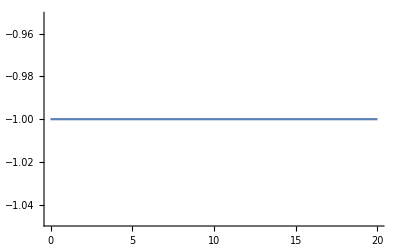

```mathematica
Plot[Re[σ1] /. {τ->1, λ->1, a->0}, {tBar, 0, 20}]
```

Without activity, zero k flow seems to always be stable.

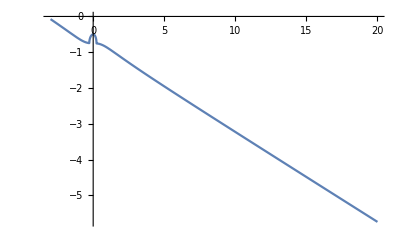

```mathematica
Plot[Re[σ1] /. {τ->1, λ->1, a->0.5}, {tBar, -3, 20}]
```

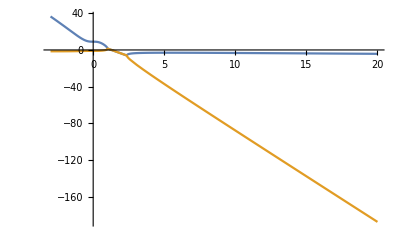

```mathematica
Plot[{Re[σ1] /. {τ->1, λ->1, a->10}, Re[σ2] /. {τ->1, λ->1,a->10}}, {tBar, -3, 20}]
```

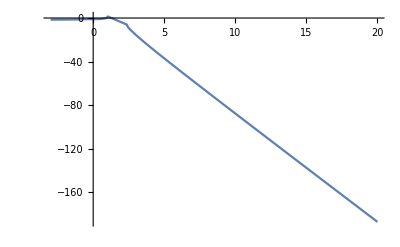

```mathematica
Plot[Re[σ2] /. {τ->1, λ->1, a->10}, {tBar, -3, 20}]
```

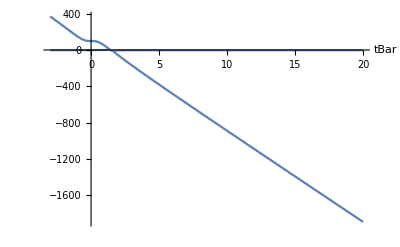

```mathematica
Plot[{Re[σ1],Re[σ2]} /. {τ->1, λ->1, a->100},{tBar, -3, 20}, AxesLabel->Automatic]
```

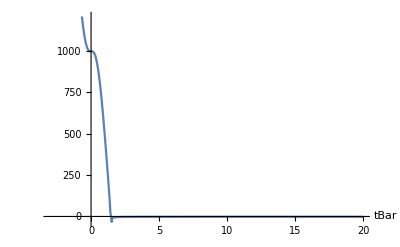

```mathematica
Plot[Re[σ1] /. {τ->1, λ->1, a->1000}, {tBar, -3, 20}, AxesLabel->Automatic]
```

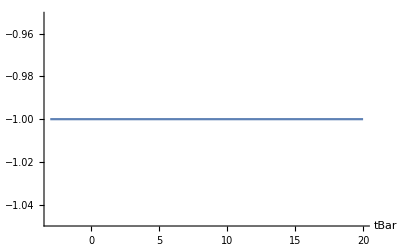

```mathematica
Plot[Re[σ2] /. {τ->1,λ->1,a->0}, {tBar,-3,20}, AxesLabel->Automatic]
```

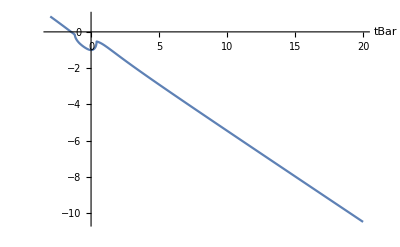

```mathematica
Plot[Re[σ2] /. {τ->1,λ->1,a->1}, {tBar,-3,20}, AxesLabel->Automatic]
```

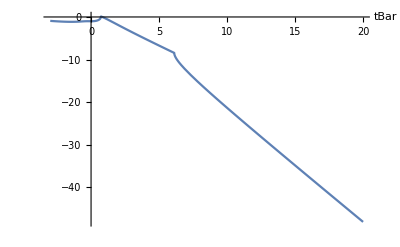

```mathematica
Plot[Re[σ2] /. {τ->1,λ->1,a->3}, {tBar,-3,20}, AxesLabel->Automatic]
```

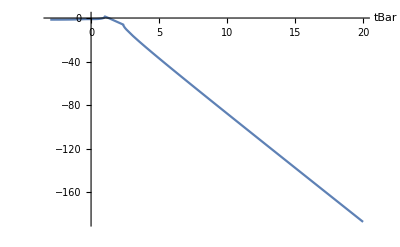

```mathematica
Plot[Re[σ2] /. {τ->1,λ->1,a->10}, {tBar,-3,20}, AxesLabel->Automatic]
```

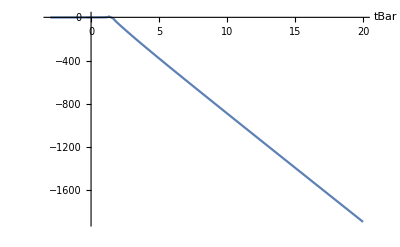

```mathematica
Plot[Re[σ2] /. {τ->1,λ->1,a->100}, {tBar,-3,20}, AxesLabel->Automatic]
```